```mathematica
Задание 1;
f[x_,y_]:=x*y*Log[x^2+y^2]
```

```mathematica
Plot3D[f[x,y],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
h1=ContourPlot[f[x,y],{x,-0.8,0.8},{y,-0.8,0.8}];
```

```mathematica
h2=VectorPlot[Evaluate[Grad[f[x,y],{x,y}]],{x,-0.8,0.8},{y,-0.8,0.8}];
```

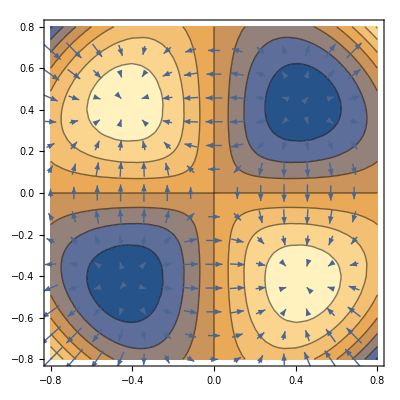

```mathematica
Show[h1,h2]
```

```mathematica
FindMinimum[f[x,y],{x,-0.5},{y,-0.4}]
```

{-0.18394,{x→-0.428882,y→-0.428882}}

```mathematica
FindMaximum[f[x,y],{x,-0.4},{y,0.4}]
```

{0.18394,{x→-0.428882,y→0.428882}}

```mathematica
Задание 2;
```

```mathematica
r1=ImplicitRegion[x≤1&&y≤1,{x,y}];
```

```mathematica
r2=ImplicitRegion[y≥(x-1)^2,{x,y}];
```

```mathematica
r3=RegionIntersection[r1,r2];
```

```mathematica
g[x_,y_]:=x^2+x+2y
```

```mathematica
NMaximize[{g[x,y],{x,y}∈r3},{x,y}]
```

{4.,{x→1.,y→1.}}

```mathematica
NMinimize[{g[x,y],{x,y}∈r3},{x,y}]
```

{1.25,{x→0.500002,y→0.249998}}

```mathematica
h[x_,y_]:=(x+y)ⅇ^(-(x+2y))
```

```mathematica
t1=ImplicitRegion[x>0&&y>0,{x,y}];
```

```mathematica
NMaximize[{h[x,y],{x,y}∈t1},{x,y}]
```

{1.42802×10^-15,{x→6.43887,y→15.414}}

```mathematica
NMinimize[{h[x,y],{x,y}∈t1},{x,y}]
```

{0.,{x→93143.4,y→100608.}}

```mathematica
Задание 3(б);
```

```mathematica
f[x_,y_,z_]:=x^2+y^2-4z^2-1
```

```mathematica
ar1=D[f[x,y,z],x] /.x->2;
```

```mathematica
ar2=D[f[x,y,z],y]/.y->1;
```

```mathematica
ar3=D[f[x,y,z],z]/.z->1;
```

```mathematica
h[x_,y_,z_]:=ar1*(x-2)+ar2*(y-1)+ar3*(z-1)
```

```mathematica
kas=ContourPlot3D[h[x,y,z]==0,{x,-10,10},{y,-10,10},{z,-10,10},ContourStyle->Red];
```

```mathematica
func=ContourPlot3D[f[x,y,z]==0,{x,-10,10},{y,-10,10},{z,-10,10}];
```

```mathematica
Show[kas,func]
```

-Graphics3D-

```mathematica
Задание 3(а)
```

```mathematica
z[x_,y_]:=ⅇ^(y^2+2x-1)
```

```mathematica
mn1=D[z[x,y],x]/.{x->1,y->1};
mn2=D[z[x,y],y]/.{x->1,y->1};
```

```mathematica
z0=z[1,1];
```

```mathematica
Plos[x_,y_]:=mn1*(x-1)+mn2*(y-1)+z0
```

```mathematica
Kasat=Plot3D[Plos[x,y],{x,-5,5},{y,-5,5},PlotStyle->Red];
```

```mathematica
Pover=Plot3D[z[x,y],{x,-5,5},{y,-5,5}];
```

```mathematica
Show[Kasat,Pover]
```

-Graphics3D-

```mathematica
Series[z[x,y],{x,1,5},{y,1,5}]
```

(ⅇ^2+2 ⅇ^2 (y-1)+3 ⅇ^2 (y-1)^2+10/3 ⅇ^2 (y-1)^3+19/6 ⅇ^2 (y-1)^4+13/5 ⅇ^2 (y-1)^5+O[y-1]^6)+(2 ⅇ^2+4 ⅇ^2 (y-1)+6 ⅇ^2 (y-1)^2+20/3 ⅇ^2 (y-1)^3+19/3 ⅇ^2 (y-1)^4+26/5 ⅇ^2 (y-1)^5+O[y-1]^6) (x-1)+(2 ⅇ^2+4 ⅇ^2 (y-1)+6 ⅇ^2 (y-1)^2+20/3 ⅇ^2 (y-1)^3+19/3 ⅇ^2 (y-1)^4+26/5 ⅇ^2 (y-1)^5+O[y-1]^6) (x-1)^2+((4 ⅇ^2)/3+8/3 ⅇ^2 (y-1)+4 ⅇ^2 (y-1)^2+40/9 ⅇ^2 (y-1)^3+38/9 ⅇ^2 (y-1)^4+52/15 ⅇ^2 (y-1)^5+O[y-1]^6) (x-1)^3+((2 ⅇ^2)/3+4/3 ⅇ^2 (y-1)+2 ⅇ^2 (y-1)^2+20/9 ⅇ^2 (y-1)^3+19/9 ⅇ^2 (y-1)^4+26/15 ⅇ^2 (y-1)^5+O[y-1]^6) (x-1)^4+((4 ⅇ^2)/15+8/15 ⅇ^2 (y-1)+4/5 ⅇ^2 (y-1)^2+8/9 ⅇ^2 (y-1)^3+38/45 ⅇ^2 (y-1)^4+52/75 ⅇ^2 (y-1)^5+O[y-1]^6) (x-1)^5+O[x-1]^6

```mathematica
u[x_,y_]:=x^2+y^2
```

```mathematica
NMaximize[u[x,y],(x^2/4)+y^2==1,{x,y}]
```

{4.,{x→2.,y→-9.51112×10^-14}}